In this notebook we derive some of the mathematical tools we used to analyze the adaptive dynamics of our model. In particular, we derive explicit expressions for invasion fitness, for the selection gradient and for the curvature of the fitness function. Other derivations are presented in the manuscript.

The model

The model is as follows:

```mathematica
(* Transition matrix *)
Λ=S.M.R;

(* Survival matrix *)
S=({{Subscript[s, 1], 0}, {0, Subscript[s, 2]}});

(* Migration matrix *)
M=({{1-m, m}, {m, 1-m}});

(* Reproduction matrix *)
R=({{Subscript[r, 1], 0}, {0, Subscript[r, 2]}});

(* Reproduction function *)
Subscript[r, 1][x_]:=Piecewise[{{Subscript[r, max],Subscript[w, 1][x]>c Subscript[r, max]},{Subscript[w, 1][x]/c,Subscript[w, 1][x]>0}},0];
Subscript[r, 2][x_]:=Piecewise[{{Subscript[r, max],Subscript[w, 2][x]>c Subscript[r, max]},{Subscript[w, 2][x]/c,Subscript[w, 2][x]>0}},0];

(* Survival function *)
Subscript[s, 1][x_]:=1/(1+Exp[-a Subscript[w, 1][x]]);
Subscript[s, 2][x_]:=1/(1+Exp[-a Subscript[w, 2][x]]);

(* Water surplus *)
Subscript[w, 1][x_]:=Subscript[W, 1]/Subscript[n, 1]-x;
Subscript[w, 2][x_]:=Subscript[W, 2]/Subscript[n, 2]-x;
```

#### Population dynamics

Here we have a look at what the population dynamics of our model look like under a fixed set of parameters, e.g.

```mathematica
(* Example parameter set *)
pars={m->0.5,Subscript[W, 1]->600,Subscript[W, 2]->100,c->1,a->5,Subscript[r, max]->3};
```

We then evaluate the population densities in the two patches at various time steps given a trait value and some initial conditions.

```mathematica
(* Rule to make the equations explicit *)
expl={Subscript[s, 1]->Subscript[s, 1][x],Subscript[s, 2]->Subscript[s, 2][x],Subscript[r, 1]->Subscript[r, 1][x],Subscript[r, 2]->Subscript[r, 2][x]};

(* Equations describing the dynamics *)
eq={Subscript[n, 1][t+1],Subscript[n, 2][t+1]}==(Λ/.expl/.{Subscript[n, 1]->Subscript[n, 1][t],Subscript[n, 2]->Subscript[n, 2][t]}).{Subscript[n, 1][t],Subscript[n, 2][t]}/.pars/.x->0;

(* Initial conditions *)
init={Subscript[n, 1][0]==1,Subscript[n, 2][0]==1};
```

Now evaluate.

```mathematica
(* Numerical evaluation *)
tab=RecurrenceTable[{eq,init},{Subscript[n, 1],Subscript[n, 2]},{t,0,49}];
```

And plot.

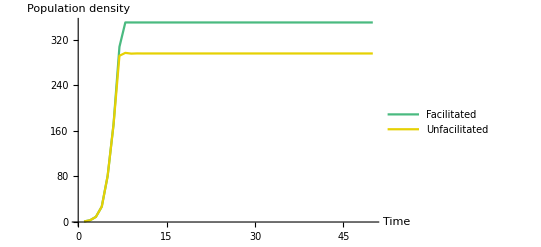

```mathematica
(* Plotting *)
ListLinePlot[Transpose[tab],PlotStyle->{RGBColor[0.29,0.73,0.5],RGBColor[0.9,0.82,0.01]},PlotRange->Full,PlotLegends->{"Facilitated","Unfacilitated"},AxesLabel->{"Time","Population density"}]
```

### Invasion fitness

Next, we compute the invasion fitness of the mutant as the leading eigenvalue of the transition matrix.

```mathematica
λ=Λ//Eigenvalues//Last
```

1/2 (r_1 s_1-m r_1 s_1+r_2 s_2-m r_2 s_2+√((-r_1 s_1+m r_1 s_1-r_2 s_2+m r_2 s_2)^2-4 (r_1 r_2 s_1 s_2-2 m r_1 r_2 s_1 s_2)))

We now check that the invasion fitness is indeed one when evaluated at the resident, i.e. when the mutant is the resident, under a random set of parameter values.

For this we need to find the equilibrium population densities given the parameters (we do that numerically).

```mathematica
(* Find equilibrium densities *)
eq={Subscript[n, 1],Subscript[n, 2]}==Λ.{Subscript[n, 1],Subscript[n, 2]}/.expl;
sol=FindRoot[eq/.pars/.x->4,{{Subscript[n, 1],5000},{Subscript[n, 2],5000}}]
```

FindRoot::nlnum: The function value … is not a list of numbers with dimensions {2} at {n_1,n_2} = {5000.,5000.}.

FindRoot[eq/.pars/.x→4,{{n_1,5000},{n_2,5000}}]

Then, we plug those equilibrium densities into the invasion fitness function, with the rest of the parameters.

```mathematica
(* Invasion fitness of the resident *)
λ/.Subscript[p, 1]->p[x,Subscript[θ, 1]]/.Subscript[p, 2]->p[x,Subscript[θ, 2]]/.Subscript[q, 1]->Subscript[q, 1][x]/.Subscript[q, 2]->Subscript[q, 2][x]/.pars/.sol/.x->4
```

1.

Now that we have the invasion fitness, we want to get a formula for the selection gradient, which will help us identify singular strategies and long-term evolutionary equilibria.